## Slide 1

## Some Miscellaneous Adventures in

# Experimental Mathematical Physics

## Reed College Physics Seminar 9 November 2011

## Nicholas Wheeler A. A. Knowlton Professor (Emeritus)

## Slide 2

## Slide 3

# 1. Patterned Spectra of Large Random Matrices

One of the central figures in 20^thCentury mathematical physics was a woman named Magrit, known to her intimates as Manci. For she was the wife of

Paul Adrien Maurice Dirac (1902 - 1984)  : Nobel Prize 1933

and the sister of

Eugene Paul Wigner (1902 - 1995) : Nobel Prize 1963

It was reportedly Dirac's habit to introduce his wife as "Wigner's sister." Here she is (1963) with her husband:

## Slide 4

Wigner was born in Budapest, developed an interest in mathematics while recovering (age 11) from tuberculosis at a mountain retreat in Austria, was profoundly influenced—as was his classmate, John von Neumann—by Lászió Rátz, his "greatest teacher," who taught mathematics in the gymnasium which both attended. At college in Berlin he majored in chemical engineering, but attended the Wednesday afternoon seminars that featured speakers like Planck, von Laue, Heisenberg, Nernst, Pauli, Einstein, and was motivated to take up (mathematical) physics as a career.  At Göttingen he worked as an assistant to Hilbert, worked later at Princeton, University of Wisconsin, Princeton again, and finally at the University of Texas.

Wigner's name is attached to a great and diverse number of fundamental developments, of which I present a very incomplete list:

   • applications of group theory to quantum mechanics
   • phase space formulation of quantum mechanics (Wigner quasi-probability distribution)
   • connection between particle physics and representations of the Lorentz group
   • exploration of symmetry principles and the manifestations of broken symmetry
   • contributions to pure/applied nuclear physics
   • "Unreasonable effectiveness of mathematics in the natural sciences"
   • the Wigner semicircle distribution

Wigner's Nobel Prize—which he shared with Maria Goeppert Mayer & J. Hans Jensen, who made "discoveries concerning nuclear shell structure"—recognized his "contributions to the theory of the atomic nucleus and the elementary particles, particularly through the discovery and application of fundamental symmetry principles." It was a pretty contribution to nuclear theory that provided my point of departure.

## Slide 5

Here is a table of nuclides

```mathematica
Hyperlink["Table of Nuclides","http://en.wikipedia.org/wiki/Table_of_nuclides_(complete)"]
```

each of which presents a many-body quantum system with unknown Hamiltonian. One has interest in the energy levels, and (more particularly) the differences between energy levels.  In 1954, Wigner was led to ask

"What can one say concerning the statistical properties of the spectra of very large hermitian (or real symmetric) matrices?" 

Heavy analysis—unsupported by a shred of numerical evidence—led Wigner to the famously pretty (and quite unanticipated) result reported in "Characteristic vectors of bordered matrices in infinite dimensions," Annals of Mathematics 62, 548 - 564 (1955)…or which more in a moment.

On Saturday, 6 February 2010, it was my job to administer the Junior Qual. I therefore found myself obliged to remain close to my office for six hours. I elected—as an amusing passtime, and for no particular reason—to use the time to see what the numerical resources of Mathematica might have to say about the answer to Wigner's question.

## Slide 6

Computing/plot the eigenvalues of a population of ten thousant 10 × 10 symmetric matrices, with elements drawn randomly from the unit interval [0, 1]

```mathematica
EigenvalueList10=Flatten[Table[Chop[Eigenvalues[(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[{},{10,10}]]],{k,1,10000}]];
ListPlot[EigenvalueList10,PlotRange->{-2,10}]
```

Was surprised to see that the eigenvalues are resolved into two distinct populations. To clarify the situation, I looked to a smaller population of such matrices :

```mathematica
ShortEigenvalueList10=Flatten[Table[Chop[Eigenvalues[(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[{},{10,10}]]],{k,1,20}]];
DisplayEigenvalues10=ListPlot[ShortEigenvalueList10,PlotRange->{-2,10}]
```

Mentioned this development to Lucas Illing, who immediately directed my attention to a classic result obtained by Oskar Perron (1907) & Georg Frobenius (1912). Google supplies links to a large and diverse collection of sites. The Wikipedia site is useful, but is for some reason invisible to Mathematica. As an alternative, see

```mathematica
Hyperlink["Perron-Frobenius Theorem","http://www.stanford.edu/class/ee363/lectures/pf.pdf"]
```

The theorem—which has been now been established by a great assortment of methods, and is central to the solution of a great assortment of pure/applied problems—asserts that if the elements of the real square matrix 𝕄 are all positive, then
   • the leading eigenvalue is invariably real and unique (non - degenerate)
   • the associated eigenvector is unique in that all of its elements have the same sign.
For a simple proof (that assumes symmetry of the positive matrix) see

```mathematica
Hyperlink["Ninio's Proof","http://lptms.u-psud.fr/membres/trizac/Ens/M2MQ/Ninio_PerronFro.pdf"]
```

I happened at this point to be browsing in M. Aigner & G. M. Ziegler's Proofs from THE BOOK (1998) where I came upon a result due to Legendre—presented there as a consequence of the inequalities

harmonic mean ⩽ geometric mean ⩽ arithmetic mean

THEOREM: Suppose all roots of the polynomial

x^n+a_(n-1)x^(n-1)+a_(n-2)x^(n-2) ... +a_0

are real. Then the roots are contained in the interval with endpoints

-(a_(n-1))/n± (n-1)/n √((a_(n-1))^2-(2n)/(n-1)a_(n-2))

from which I was able to extract this

COROLLARY: Let 𝕏 be a d-dimensional real symmetric matrix. Then the spectrum of 𝕏 lies within the interval bounded by

```mathematica
upper[𝕏_,d_]:=Tr[𝕏]/d+ (d-1)/d √((d Tr[𝕏.𝕏]-Tr[𝕏]^2)/(d-1))
lower[𝕏_,d_]:=Tr[𝕏]/d- (d-1)/d √((d Tr[𝕏.𝕏]-Tr[𝕏]^2)/(d-1))
```

Tom Wieting was able to extract these bounds from the Cayley-Schwarz inequality, and to phrase them as a relationships between the spectral mean and spectral variance.

Here I compare those bounds with the spectra of a randomly generated 20-member population of 
10 × 10 real symmetric matrices:

```mathematica
Table[Subscript[𝔸, k]=(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[{},{10,10}],{k,1,20}];
Fig1=ListPlot[Flatten[Table[{upper[Subscript[𝔸, k],10],Eigenvalues[Subscript[𝔸, k]],lower[Subscript[𝔸, k],10]},{k,1,20}]], PlotRange->{-6,7},
PlotStyle->{Blue,PointSize[0.01]}];
Fig2=ListPlot[Flatten[Table[{upper[Subscript[𝔸, k],10],{8,8,8,8,8,8,8,8,8,8},lower[Subscript[𝔸, k],10]},{k,1,20}]], PlotRange->{-6,7}, PlotStyle->{Red,PointSize[0.015]}];

Show[{Fig1, Fig2}]
```

Note that the leading eigenvalue lies in all cases quite near the bound set by the COROLLARY.

## Slide 7

If one violates the Perron-Frobenius positivity requirement the outlier eigenvalues are found to disappear. Adopting three different distributions (uniform, triangular & normal)—all callibrated to have zero means and unit variances

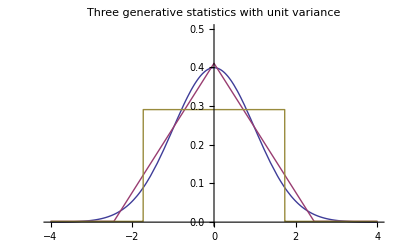

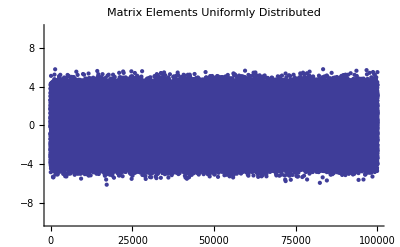

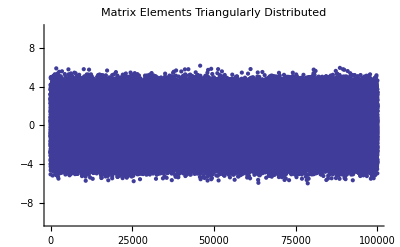

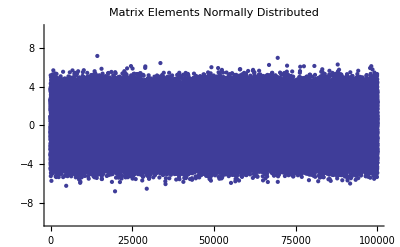

#### Uniformity of spectral bounds

I construct 500-member populations of random matrices of dimensions 10, 20, 40, 80 and plot their minimal/maximal eigenvalues:

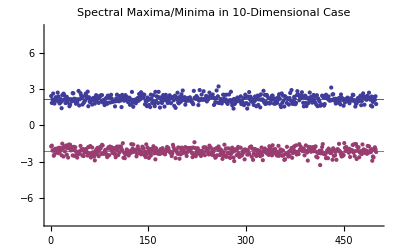

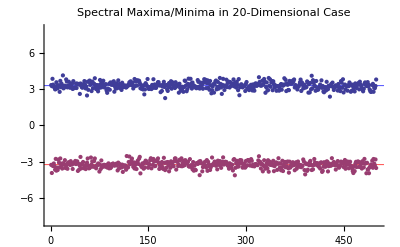

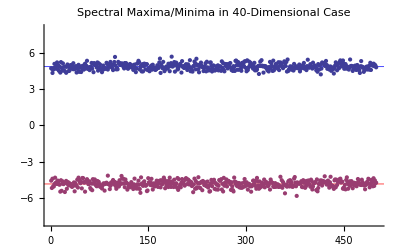

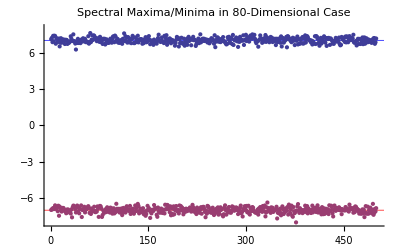

Numerical experiments indicate that
   • Mean spectral bounds are proportional to the standard deviation of the generative statistic
     (whatever it may be);
   • Mean spectral bounds are (in a non-linear way that varies from statistic to statistic) slowly
     increasing functions of dimension;
   • Spectral bound variance is a slowly decreasing function of dimension.

Which is our first hint that patterns become simpler and more regular as dimension increases.

## Slide 8

### Spectral Distribution

Conflate the spectra of the Nn eigenvalues of an N-member population of n × n matrices, partition the interval [spectral minimum, spectral maximum] into bins, count the number of eigenvalues that fall into each bin and divide by Nn to obtain spectral distribution function—the probability p_i that an eigenvalue, selected at random, will be found to occupy the i^th bin.

10,000-member population of 10 × 10 matrices:

We have here a collection of 100,000 eigenvalues, all of which lie interior to the interval  [-3.7, 3.7]. Partitioning the interval into 148 bins, each of width 0.05, we are led to the following figure:

```mathematica
EigenvalueSet10=Flatten[Table[Eigenvalues[(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[UniformDistribution[{-1,1}],{10,10}]],{k,1,10000}]];
RawBinCounts10=BinCounts[EigenvalueSet10,{-3.7,3.7,0.05}];
BinProbabilities10=N[RawBinCounts10/100000];
ShowBinProbatilities10=ListPlot[BinProbabilities10,Ticks->{{Length[RawBinCounts10]/2,Length[RawBinCounts10]}},AxesLabel->{"Bin Number"},PlotLabel->"Probability of Bin Occupancy, 10-Dimensional Case" ]
```

5,000-member population of 20 × 20 matrices:

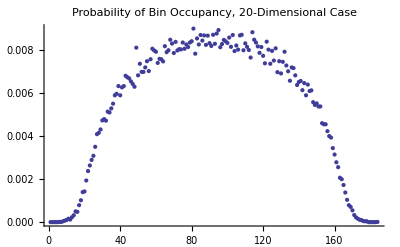

1000-member population of 100 × 100 matrices:

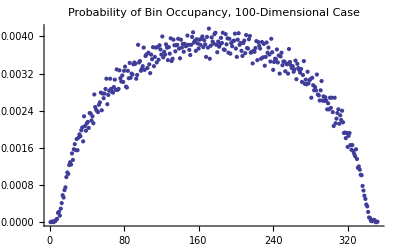

## Slide 9

Again, we notice a trend toward simpler and more regular structure as dimension increases: those "sombrero distributions" lose their brims as  N → ∞, and bring to mind the

semicircular distribution = semicircle/area

For random variables that range on [0, B] we have

```mathematica
S[x_,B_]:=8/(π B^2)√(x(B-x))

Manipulate[Plot[S[x,B],{x,0,B}, AspectRatio->Automatic, PlotRange->{{0,2},{0,2}},PlotStyle->{Thick}, PlotLabel->"Semicircular Distributions"],{B,.7,2}]
```

Here we attempt to fit the semicircular distribution to data generated in the 10-dimensional case:

```mathematica
SemiCircularDistribution10=Plot[S[x,148],{x,0,148},PlotStyle->{Thick, Red}];

Show[{ShowBinProbatilities10,SemiCircularDistribution10}]
```

The fit is spectacularly poor, a casualty of the presence of "sombrero brims;" i.e., of the relatively small number of eigenvalues that lie near the spectral bounds. But when we look to the eigenvalues of a 100-member population of 1000  × 1000 similarly-generated matrices

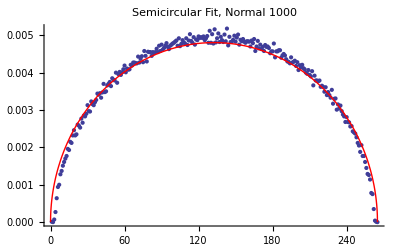

we find that the "brim problem" has pretty much evaporated, and the trend  N → ∞ is clear.

We have arrived computationally at the result which Wigner obtained analytically. The discovery of Wigner's semicircle law has given rise to an enormous (and still-expanding) literature (to which Freeman Dyson was an important early contributor). The theory of random matrices has been found to have important applications to (among other fields)
   •  the theory of disordered solid state and chaotic systems;
   •  statistical mechanics
   •  physics of superconductivity, quantum dots 
   •  quantum field theory
   •  signal processing
   •  design of web search engines
   •  number theory
   •  the mathematics of graph theory, group theory, orthogonal polynomials, integral  equations, 
      non-commutative probability theory, combinatorics, random partitions, …
      
See, for example, M. L. Mehta, Random Matrices (1991) for a comprehensive review.

## Slide 10

```mathematica
Spectral distributions of large supersymmetric matrices
```

Have looked thus far to the symmetric parts of large random matrices:

"Symmetric Part" Matrices=(𝕄^transpose+𝕄)/2

There exists an alternative way to generate symmetric matrices:

"Supersymmetric" Matrices=𝕄^transpose.𝕄

Such matrices—which are square even when 𝕄 is rectangular— are called "Wishart matrices" (in honor of John Wishart, who studied statistical aspects of such matrices—including their spectral distribution—already in 1928, nearly 30 years before Wigner entered the random matrix picture) by mathematicians: my own "supersymmetric" terminology derives from the fact that operators of the form 𝕒^transpose.𝕒, which entered physics via Dirac's algebraic formulation of quantum oscillator theory, are fundamental to supersymmetric quantum field theory, and—Witten's simplification of that subject—to supersymmetric quantum mechanics.

It follows immediately from

```mathematica
(𝕄^transpose).𝕄 ψ=λ ψ
```

that the eigenvalues of supersymmetric matrices are necessarily non-negative. We  look to the eigenvalues of a 10,000-member population of 10 × 10 supersymmetric matrices:

```mathematica
EigenvalueListSupersymmetric10=Flatten[Table[Chop[Eigenvalues[𝕄.Transpose[𝕄]/.𝕄->RandomReal[NormalDistribution[0,1],{10,10}]]],{k,1,1000}]];
ListPlot[EigenvalueListSupersymmetric10,PlotRange->{-1,100},GridLines->{{},{40}}, GridLinesStyle->Directive[Red, Thick]]
```

Remarkably, the spectra of such matrices do NOT conform to Wigner's Semicircle Law:

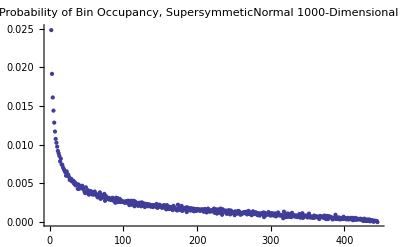

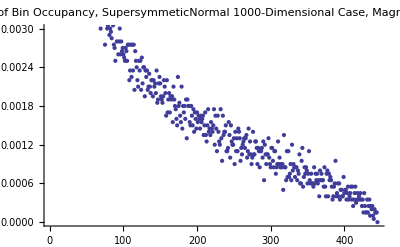

Analytical work by Vladimir Marchenko and Leonid Pastur (1967) led to the Marchenko-Pastur Law:

LP[x,B]=2/(π B)√((B-x)/x)   :   0⩽ x ⩽ B

Here are views of how a suitably selected Marchenko-Pastur distribution conforms to data:

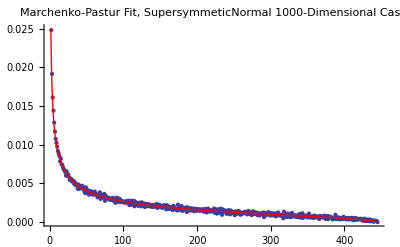

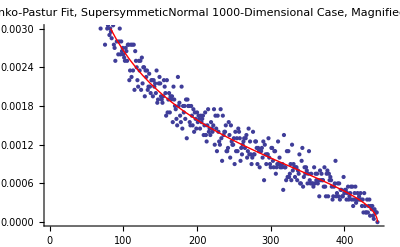

## Slide 11

```mathematica
Unification: The Beta Distributions
```

It is an awkward fact that one cannot fit a Gaussian wavepacket into a box (the wings overextend the bounds of the box). It was in this connection that I first encountered the beta distribution, which is actually a 2-parameter class of distributions that live naturally on the unit interval. It is defined

```mathematica
PDF[BetaDistribution[α,β],x]
```

where α and β can assume any positive real values, and where Beta[α, β] is the Euler beta function:

Beta[α,β]=(Γ[α]Γ[β])/Γ[α+β]

```mathematica
Subscript[μ, Wigner][x_,B_]:=8/(π B^2)√(x(B-x))
```

```mathematica
Subscript[μ, Marchenko-Pastur][x_,B_]:=2/(π B)√((B-x)/x)
```

```mathematica
Assuming[{B>0,x>0},Simplify[Subscript[μ, Wigner][x,B]==1/B PDF[BetaDistribution[3/2,3/2],x/B]]]
```

```mathematica
Assuming[{B>0,x>0},Simplify[Subscript[μ, Marchenko-Pastur][x,B]==1/B PDF[BetaDistribution[1/2,3/2],x/B]]]
```

My hunch that the beta distribution could be made to account for the sombrero distributions that arise from low-dimensional random matrices turned out to be ill-founded. The Wigner and Marchenko-Pastur laws pertain only to the spectra of asymptotically large matrices; matrices of finite dimension pose a more difficult problem.

## Slide 12

# 2. Random Walks

### Simple Random Walks on the 2D Plane

```mathematica
LatticeSteps=Join[{{0,0}},Table[{Cos[α], Sin[α]}/.{α->π/2 RandomChoice[{0,1,2,3}]},{n,1,500}]];
SuccessiveLatticePositions=Table[∑_(k=1)^m LatticeSteps⟦k⟧, {m,1,500}];
LatticeWalk=Graphics[{{Red,Line[SuccessiveLatticePositions]},{{PointSize[.02],Point[First[SuccessiveLatticePositions]]}},
{{PointSize[.02],Red,Point[Last[SuccessiveLatticePositions]]}}},Axes->True ,PlotLabel->"Drunkard's Walk"]
```

```mathematica
Steps1=Table[{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
Steps2=Table[{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
Steps3=Table[{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
Steps4=Table[{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
SuccessivePositions1=Table[∑_(k=1)^m Steps1⟦k⟧, {m,1,1000}];
SuccessivePositions2=Table[∑_(k=1)^m Steps2⟦k⟧, {m,1,1000}];
SuccessivePositions3=Table[∑_(k=1)^m Steps3⟦k⟧, {m,1,1000}];
SuccessivePositions4=Table[∑_(k=1)^m Steps4⟦k⟧, {m,1,1000}];
RandomWalk1=Graphics[{Black,Line[SuccessivePositions1]}];
RandomWalk2=Graphics[{Red,Line[SuccessivePositions2]}];
RandomWalk3=Graphics[{Blue,Line[SuccessivePositions3]}];
RandomWalk4=Graphics[{Green,Line[SuccessivePositions4]}];

CircularGrid=Graphics[{Circle[{0,0},√100],Circle[{0,0},√200],Circle[{0,0},√300],Circle[{0,0},√400],Circle[{0,0},√500],Circle[{0,0},√600],Circle[{0,0},√700],Circle[{0,0},√800],Circle[{0,0},√900],Circle[{0,0},√1000]}];

Show[CircularGrid, RandomWalk1, RandomWalk2, RandomWalk3, RandomWalk4,Axes->True, Ticks->False]
```

The figure shows 4 random 1000-step walks, each of which begins at the origin: the steps have unit length, and the direction of each new step is random.

Theoretically, one expects to have

mean net displacement=√(number of steps)

For small samples that trend is scarcely visible (lost in the noise):

```mathematica
NetDisplacement1[n_]:=Norm[Part[SuccessivePositions1,n]]
NetDisplacement2[n_]:=Norm[Part[SuccessivePositions2,n]]
NetDisplacement3[n_]:=Norm[Part[SuccessivePositions3,n]]
NetDisplacement4[n_]:=Norm[Part[SuccessivePositions4,n]]

PlotNetDisplacement1=ListPlot[Table[NetDisplacement1[n],{n,1,1000}], Joined->True, PlotStyle->Black, PlotRange->{0,80}];
PlotNetDisplacement2=ListPlot[Table[NetDisplacement2[n],{n,1,1000}], Joined->True, PlotStyle->Red, PlotRange->{0,80}];
PlotNetDisplacement3=ListPlot[Table[NetDisplacement3[n],{n,1,1000}], Joined->True, PlotStyle->Blue, PlotRange->{0,80}];
PlotNetDisplacement4=ListPlot[Table[NetDisplacement4[n],{n,1,1000}], Joined->True, PlotStyle->Green, PlotRange->{0,80}];

ExpectedNetDisplacement=ListPlot[Table[√n,{n,1,1000}], PlotRange->{0,80}];

Show[ExpectedNetDisplacement,PlotNetDisplacement1 ,PlotNetDisplacement2,PlotNetDisplacement3,PlotNetDisplacement4]
```

but for asymptotically large samples ( ~ Avagadro's Number^(2/3)~ 10^16 ) one expects the N-step end-point distribution to be bi-variate Gaussian

ρ_normal[x, y, N]:=(ⅇ^(-(x^2+y^2)/(2N)))/(N √(2 π))

and to satisfy the diffusion equation

1/2(∂_(x,x) +∂_(y,y))ρ_normal=∂_N ρ_normal

But reproducing ρ_normal by such a Monte-Carlo technique would, as I have indicated, be computationally very expensive.

## Slide 13

```mathematica
Strange Random Walks on the 2D Plane
```

In some biophysical, hydrological, financial…contexts one encounters walks in which the generative distribution has a long tail, giving rise to occasional unexpectedly long steps. The resulting walks ("Lévy flights") look strange

```mathematica
Plot[PDF[FRatioDistribution[3,4.1],x],{x,0,5}]
```

```mathematica
Mean[FRatioDistribution[3,4.1]]
StandardDeviation[FRatioDistribution[3,4.1]]
```

```mathematica
LevySteps1=Table[RandomReal[FRatioDistribution[3,4.1]]{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
LevySteps2=Table[RandomReal[FRatioDistribution[3,4.1]]{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
LevySteps3=Table[RandomReal[FRatioDistribution[3,4.1]]{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
LevySteps4=Table[RandomReal[FRatioDistribution[3,4.1]]{Cos[α], Sin[α]}/.{α->2π RandomReal[]},{n,1,1000}];
SuccessiveLevyPositions1=Table[∑_(k=1)^m LevySteps1⟦k⟧, {m,1,1000}];
SuccessiveLevyPositions2=Table[∑_(k=1)^m LevySteps2⟦k⟧, {m,1,1000}];
SuccessiveLevyPositions3=Table[∑_(k=1)^m LevySteps3⟦k⟧, {m,1,1000}];
SuccessiveLevyPositions4=Table[∑_(k=1)^m LevySteps4⟦k⟧, {m,1,1000}];
RandomLevyWalk1=Graphics[{Black,Line[SuccessiveLevyPositions1]}];
RandomLevyWalk2=Graphics[{Red,Line[SuccessiveLevyPositions2]}];
RandomLevyWalk3=Graphics[{Blue,Line[SuccessiveLevyPositions3]}];
RandomLevyWalk4=Graphics[{Green,Line[SuccessiveLevyPositions4]}];

Show[RandomLevyWalk1, RandomLevyWalk2, RandomLevyWalk3, RandomLevyWalk4,Axes->True, Ticks->False]
```

Random walks of this type give rise to "super-diffusion," and to a distribution function that satisfies a fractional diffusion equation

1/2(∂_(x,x) +∂_(y,y))ρ_super=(∂_N)^fractional ρ_super

## Slide 14

Strange Random Walks on the Line

Suppose step length is subject to power-law graduation

Length of n^th step=s^n

```mathematica
MaxDisplacement[N_]:=∑_(n=0)^(N-1) s^n
MaxDisplacement[N]
```

```mathematica
Assuming[0<s<1,Limit[MaxDisplacement[N],N->Infinity]]
```

"Graduated one-dimensional random walks" stand evidently in very close relation to (and serve to illuminate) the mathematical theory of convergent/divergent power series.

### One-dimensional "Golden Walks"

Following P. L. Krapivsky & S. Redner, "Random walk with shrinking steps," AJP 72, 591-598 (2004) set

```mathematica
s=1/GoldenRatio//N
```

This "most irrational number" arises in innumerable mathematical & physical connections:

```mathematica
Table[Fibonacci[k]/Fibonacci[k+1],{k,1,20,5}]
N[%]
```

The asymptotically maximal displacement is

```mathematica
1/(1-s)
```

Confine attention to 20-step walks to avoid intrusion of numerical imprecisions; maximal displacement becomes

```mathematica
∑_(k=0)^19 s^k
```

For a typical 20-step walk get

```mathematica
Typical20StepDisplacement=∑_(n=0)^19 RandomChoice[{0,1}] s^n
```

Plot displacements achieved by 2,000,000 such 20-step walks:

SetOfGoldenDisplacements20=Table[∑_(n=0)^19 RandomChoice[{0,1}]s^n,{2000000}];

BinCountsGolden20=BinCounts[SetOfGoldenDisplacements20,{0,2.62,0.005}];

ListLinePlot[BinCountsGolden20, Filling→Axes,AxesLabel→{"Bin Number","Bin Count"},Ticks→{{262,524},{1000,2000,3000,4000,5000,6000,7000}}]

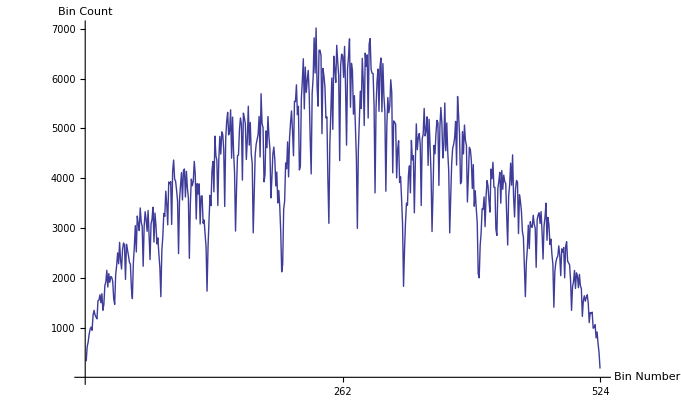

GoldenMean magic makes it possible to account analytically for every detail of that curve. Recent work indicates that

   •  if 0<s<1/2 the maximal advance distribution is fractal;
   •  if s=1/2 the distribution is uniform;
   •  if 1/2<s<1 the distribution is continuous (but shape generally unknown).

### Stretched walks

Assume s to be slightly greater than unity.  Then steps become progressively longer (not shorter), and the maximal N-step advance grows without bound as N⟶∞.  For every finite N there does, however, exist a well-defined upper bound. 

I look specifically to  the case s = 1.01, where the maximal 20-step advance is

```mathematica
∑_(n=0)^19 1.01^n
```

SetOfStretchedStepDisplacements20=Table[∑_(n=0)^19 RandomChoice[{0,1}]1.01^n,{200000}];

BinCountsStretchedSteps20=BinCounts[SetOfStretchedStepDisplacements20,{0,22,0.005}];

ListLinePlot[BinCountsStretchedSteps20, Filling→Axes,AxesLabel→{"Bin Number","Bin Count"},PlotRange→800]

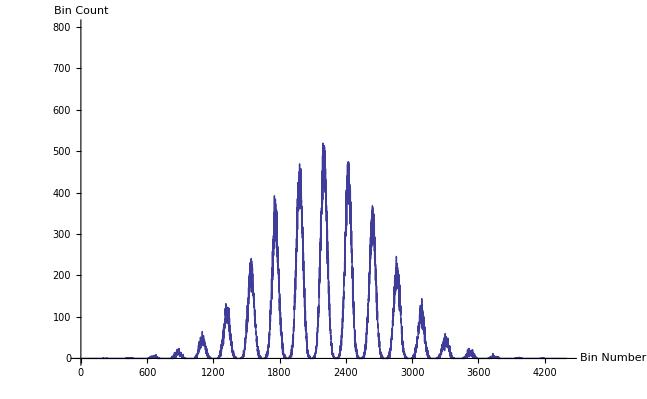

## Slide 15

```mathematica
Needs["GraphUtilities`"];
```

# 3. Random Walks on Finite Graphs

This mode of construction of the end-point distribution function is reminiscent of Feynman's sum-over-paths construction of the quantum mechanical propagator. Computationally distinct—and more "wholistic" in spirit—is the spectral construction of the quantum propagator (which presumes possession of all eigenvalues and eigenvectors of the Hamiltonian), which is analogous to the transition matrix approach to the theory of random walks, to which I now turn:

### Adjacency Matrices of Graphs

Here is a "connected graph" with 5 "vertices" and 6 connecting links, or "edges":

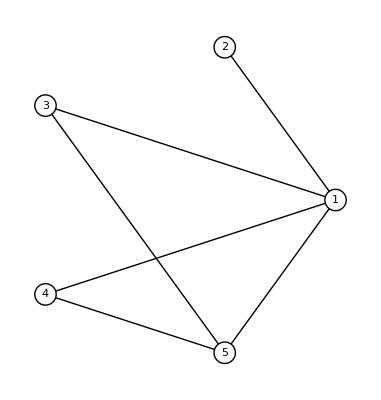

The adjacency matrix records which vertices are connected to which edges, and—since

A connected to B  ⟹ B connected to A

—is necessarily a symmetric matrix:

Associated Adjacency Matrix = (0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

Many properties of such a graph can be extracted from its adjacency matrix, which, we notice, is invariably a symmetric positive (strictly: non-negative) matrix. Look to the spectrum

```mathematica
Eigenvalues[({{0, 1, 1, 1, 1}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 1}, {1, 0, 0, 0, 1}, {1, 0, 1, 1, 0}})]//N
```

and notice that—as the Perron-Frobenious Theorem asserts—one eigenvalue is positive and much larger than the others. Look to the associated eigenvectors

```mathematica
Table[MatrixForm[N[Eigenvectors[({{0, 1, 1, 1, 1}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 1}, {1, 0, 0, 0, 1}, {1, 0, 1, 1, 0}})]]⟦k⟧],{k,1,5}]
```

and notice that—again as the Perron-Frobenious Theorem asserts—the leading eigenvector is the only one all elements of which have the same sign.

## Slide 16

### Transition Matrices & Markov Processes

Assume the walker to walk on a discrete structure—and n-point graph. Introduce a "stochastic vector"

(p_1
p_2
p_3
⋮
p_n)_N

describes the probability that after N steps the walker occupies the n^th vertex. Assume the walker to have no memory, and to base his next-step decision entirely upon probabilities associated with his immediate location

t_(i,j)=probability of transition i⟵j

Assume finally that those probabilities remain constant (are fixed features of the graph, not of the walker or his history). One has then a MARKOV PROCESS

(p_1
p_2
p_3
⋮
p_n)_(N+1)=(t_(1,1) | t_(1,2) | t_(1,3) | ⋯ | t_(1,n)
t_(2,1) | t_(2,2) | t_(2,3) | ⋯ | t_(2,n)
t_(3,1) | t_(3,2) | t_(3,3) | ⋯ | t_(3,n)
⋮ | ⋮ | ⋮ | ⋱ | ⋮
t_(n,1) | t_(n,2) | t_(t,3) | ⋯ | t_(n,n))(p_1
p_2
p_3
⋮
p_n)_N abbreviated  P_(N+1)=𝕋 P_N

where the TRANSITION MATRIX 𝕋 is a positive (non-negative) matrix with the property that the elements in each column sum to unity.

In cases in which lingering is forbidden one has

(p_1
p_2
p_3
⋮
p_n)_(N+1)=(0 | t_(1,2) | t_(1,3) | ⋯ | t_(1,n)
t_(2,1) | 0 | t_(2,3) | ⋯ | t_(2,n)
t_(3,1) | t_(3,2) | 0 | ⋯ | t_(3,n)
⋮ | ⋮ | ⋮ | ⋱ | ⋮
t_(n,1) | t_(n,2) | t_(t,3) | ⋯ | 0)(p_1
p_2
p_3
⋮
p_n)_N 

In physical statistics one frequently encounters the Principle of Detailed Balance. A Markoff process is said to be

"balanced" if 𝕋 is symmetric: probability i⟵j=probability j⟵i 
"unbalanced" otherwise

EXAMPLE: Randomly constructed unbalanced walk on a 5-point graph

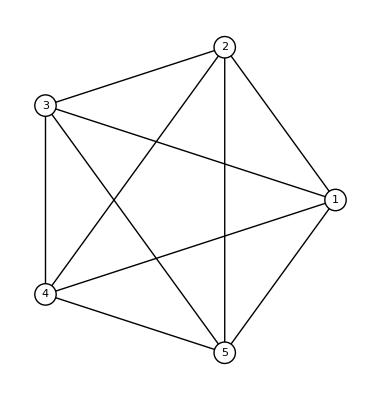

```mathematica
RowData=Table[Table[RandomReal[],{j,1,5}],{k,1,5}];
𝕋=Transpose[Table[RowData⟦k⟧/Total[RowData⟦k⟧],{k,1,5}]];
𝕋//MatrixForm
```

We check that the elements of each column do in fact add to unity (i.e., that each column vector "unitized"):

```mathematica
Table[Total[Transpose[𝕋]⟦k⟧],{k,1,5}]
```

Looking to the spectral properties of 𝕋

```mathematica
Eigenvalues[𝕋]
Abs[Eigenvalues[𝕋]]
```

we note that the leading eigenvector is unity. Also that the leading eigenvector is the only one that can be unitized

```mathematica
Table[Chop[Total[Eigenvectors[𝕋]⟦k⟧]],{k,1,5}]
```

and that the unitized leading eigenvector

```mathematica
Subscript[v, leading]=Transpose[{(Eigenvectors[𝕋]⟦1⟧)/Total[Eigenvectors[𝕋]⟦1⟧]}];
Subscript[v, leading]//MatrixForm
```

admits of interpretation as a stochastic vector (all elements non-negative).

Assuming it to be known that the walker initially occupies vertex #1, we watch the evolving state of the system:

```mathematica
P[n_]:=Transpose[MatrixPower[𝕋,n].({{1}, {0}, {0}, {0}, {0}})]⟦1⟧

EvolvingState[k_]:=Table[P[n]⟦k⟧,{n,0,10}]

ListLinePlot[{EvolvingState[1],EvolvingState[2],EvolvingState[3],EvolvingState[4],EvolvingState[5]},PlotRange->{0,1}, AxesOrigin->{1,0}]
```

we see that the system rapidly stabilizes, and that the asymptotic state is described by the leading eigenvector:

```mathematica
Table[MatrixForm[Chop[MatrixPower[𝕋,n].({{1}, {0}, {0}, {0}, {0}})-Subscript[v, leading]]],{n,0,30,10}]
```

We would have obtained the same result had we selected the initial state randomly.

## Slide 17

EXAMPLE: Randomly constructed balanced walk on a 5-point graph

```mathematica
a=Table[RandomReal[],{k,1,5}];
b=Table[RandomReal[],{k,1,4}];
c=Table[RandomReal[],{k,1,3}];
d=Table[RandomReal[],{k,1,2}];
e=Table[RandomReal[],{k,1,1}];
Subscript[Row, 1]=a/Total[a];
Subscript[Row, 2]=Join[{Subscript[Row, 1]⟦2⟧},(1-Subscript[Row, 1]⟦2⟧)/Total[b] b];
Subscript[Row, 3]=Join[{Subscript[Row, 1]⟦3⟧,Subscript[Row, 2]⟦3⟧},(1-Subscript[Row, 1]⟦3⟧-Subscript[Row, 2]⟦3⟧)/Total[c] c];
Subscript[Row, 4]=Join[{Subscript[Row, 1]⟦4⟧,Subscript[Row, 2]⟦4⟧,Subscript[Row, 3]⟦4⟧},(1-Subscript[Row, 1]⟦4⟧-Subscript[Row, 2]⟦4⟧-Subscript[Row, 3]⟦4⟧)/Total[d] d];
Subscript[Row, 5]=Join[{Subscript[Row, 1]⟦5⟧,Subscript[Row, 2]⟦5⟧,Subscript[Row, 3]⟦5⟧,Subscript[Row, 4]⟦5⟧},(1-Subscript[Row, 1]⟦5⟧-Subscript[Row, 2]⟦5⟧-Subscript[Row, 3]⟦5⟧-Subscript[Row, 4]⟦5⟧)/Total[e] e];
𝕊={Subscript[Row, 1],Subscript[Row, 2],Subscript[Row, 3],Subscript[Row, 4],Subscript[Row, 5]};

𝕊//MatrixForm
```

All eigenvalues of such a matrix are necessarily real. The leading eigenvalue is invariably unity

```mathematica
Eigenvalues[𝕊]
```

and is typically much larger than the other eigenvalues (particularly in high-dimensional cases).

The leading eigenvector

```mathematica
Subscript[u, leading]=Transpose[{First[Eigenvectors[𝕊]]/Total[First[Eigenvectors[𝕊]]]}];
Subscript[u, leading]//MatrixForm
```

is invariably "flat," and is (Perron-Frobenius) the only eigenvector of which all elements are of the same sign (and therefore—after unitization—interpretable as a stochastic vector).

Looking in such a case to the evolution of a (any) selected initial state

```mathematica
Subscript[P, balanced][n_]:=Transpose[MatrixPower[𝕊,n].({{1}, {0}, {0}, {0}, {0}})]⟦1⟧

EvolvingStateBalanced[k_]:=Table[Subscript[P, balanced][n]⟦k⟧,{n,0,10}]

ListLinePlot[{EvolvingStateBalanced[1],EvolvingStateBalanced[2],EvolvingStateBalanced[3],EvolvingStateBalanced[4],EvolvingStateBalanced[5]},PlotRange->{0,1}, AxesOrigin->{1,0}]
```

we see that asymptotically the system becomes equilibated (same probability at every vertex, because all elements of u_leading have the same value). A randomized initial state would lead ultimately to that same equilibrated asymptotic state.

## Slide 18

### Irreversible Determinism

Looking to the signs & magnitudes of the elements of

```mathematica
Inverse[𝕋]//MatrixForm
Inverse[𝕊]//MatrixForm
```

we see that the elements of those matrices cannot be assigned probabilistic interpretations.

Remarkably,

```mathematica
Table[Total[Transpose[Inverse[𝕋]]⟦k⟧],{k,1,5}]
Table[Total[Transpose[Inverse[𝕊]]⟦k⟧],{k,1,5}]
```

Circumstances such as this have led Wigner, Dirac, Feynman and many others to ask: Has "negative probability" a role to play in future physics? 

Closely related is the concept of "backward diffusion," which Richard Crandall has used to powerful effect (R. Crandall, M. McClellan, S. Arch, J. Doenias, R. Piper, "Inverse diffusion methods for data peak separation," Analytical Biochemistry 167, 15-22 (1987)). 

Reversed random walks are—though mathematically well-defined—typically not random walks in any standard sense…though in exceptional cases they may be. The randomly-constructed permutation matrix

```mathematica
ℙerm=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}});
```

is an especially simple transition matrix, and so is its inverse

```mathematica
Inverse[ℙerm]//MatrixForm
```

REMARK: Shuffling routines can be looked upon as random walks through sets of permutations.

TAKE-H0ME LESSON: IT IS FROM THE RANDOMNESS OF NATURE THAT TIME ACQUIRES ITS ARROW.

## Slide 19

### Continuous Random Walks

It is always possible (and not very difficult, if one is familiar with the "biorthogonality" concept) to write

𝕋=Exp[𝕃]

where 𝕃 us the "logarithm" of 𝕋. That done, one has

Power[𝕋,n]=Exp[n 𝕃]

which is meaningful even when n is not an integer. Mathematica knows this (is actually how Mathematica proceeds to compute powers of a matrix), so we have this smoothed version of a previous figure:

```mathematica
ContinuousP[n_]:=Transpose[MatrixPower[𝕋,n].({{1}, {0}, {0}, {0}, {0}})]⟦1⟧

ContinuouslyEvolvingState[n_,k_]:=ContinuousP[n]⟦k⟧

Plot[{ContinuouslyEvolvingState[n,1],ContinuouslyEvolvingState[n,2],ContinuouslyEvolvingState[n,3],ContinuouslyEvolvingState[n,4],ContinuouslyEvolvingState[n,5]},{n,0,10},PlotRange->{0,1}, AxesOrigin->{0,0}]
```

Similarly

```mathematica
ContinuousQ[n_]:=Transpose[Abs[MatrixPower[𝕊,n].({{1}, {0}, {0}, {0}, {0}})]]⟦1⟧

ContinuouslyEvolvingStateQ[n_,k_]:=ContinuousQ[n]⟦k⟧

Plot[{ContinuouslyEvolvingStateQ[n,1],ContinuouslyEvolvingStateQ[n,2],ContinuouslyEvolvingStateQ[n,3],ContinuouslyEvolvingStateQ[n,4],ContinuouslyEvolvingStateQ[n,5]},{n,0,10},PlotRange->{0,1}, AxesOrigin->{0,0}]
```

## Slide 20

### Entropy

The  ENTROPY  of a stochastic vector is defined

Entropy[(p_1
p_2
p_3
⋮
p_n)]=-∑_(k=1)^n p_k Log[p_k]

and provides a familiar measure of "how improbable" the distribution {p_1,p_2,p_3,...,p_n} is.

Mathematica knows that

```mathematica
Limit[-p Log[p], p->0,Direction->-1]
```

but must be told by hand what to do when it encounters expressions of the form 0 Log 0:

```mathematica
ent[x_]:=Piecewise[{{0,x==0},{-x Log[x],0<x≤1}}]
```

Looking "entropically" to the previously-encountrered equilibration process

```mathematica
P[n_]:=Transpose[MatrixPower[𝕋,n].({{1}, {0}, {0}, {0}, {0}})]⟦1⟧

EvolvingState[k_]:=Table[P[n]⟦k⟧,{n,0,10}]

ListLinePlot[{EvolvingState[1],EvolvingState[2],EvolvingState[3],EvolvingState[4],EvolvingState[5]},PlotRange->{0,1}, AxesOrigin->{1,0}]
```

we have

```mathematica
EntropyOfLeading=∑_(k=1)^5 ent[Transpose[Subscript[v, leading]]⟦1⟧⟦k⟧];ListPlot[Table[∑_(k=1)^5 ent[P[n]⟦k⟧],{n,0,10}],PlotStyle->PointSize[0.03],AxesLabel->{"Number of Iterations","Entropy"},
AxesOrigin->{1,0}, Ticks->{{},{0.5, 1.0, 1.5}},GridLines->{{},{EntropyOfLeading}}]
```

which makes vivid the meaning of "equilibration."

## Slide 21

### Maxwell's Daemon & Violation of the 2^nd Law

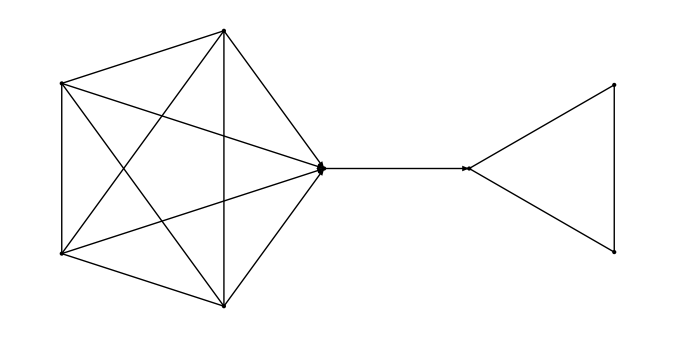

We install a one-way gate at the vertex where the 5-point graph connects to the 3-point graph.

From

```mathematica
𝔸=Transpose[ReplacePart[Transpose[𝕊],5->{0,0,0,0,0}]];
𝔸//MatrixForm
```

and

```mathematica
f=Table[RandomReal[],{k,1,3}];
g=Table[RandomReal[],{k,1,2}];
h=Table[RandomReal[],{k,1,1}];
Subscript[BRow, 1]=f/Total[f];
Subscript[BRow, 2]=Join[{Subscript[BRow, 1]⟦2⟧},(1-Subscript[BRow, 1]⟦2⟧)/Total[g] g];
Subscript[BRow, 3]=Join[{Subscript[BRow, 1]⟦3⟧,Subscript[BRow, 2]⟦3⟧},(1-Subscript[BRow, 1]⟦3⟧-Subscript[BRow, 2]⟦3⟧)/Total[h] h];
𝔹={Subscript[BRow, 1],Subscript[BRow, 2],Subscript[BRow, 3]};
𝔹//MatrixForm
```

we assemble

```mathematica
ℂ=ArrayFlatten[{{𝔸,({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}})},{({{0, 0, 0, 0, 1}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}}),𝔹}}];
ℂ//MatrixForm
```

Note that the elements of each column now once again do sum to unity. From the spectrum

```mathematica
Eigenvalues[ℂ]//Chop
```

we know at once that the system does equilibrate, and that the equilibrated state is described by the stochastic vector

```mathematica
w=Transpose[{Chop[First[Eigenvectors[ℂ]]]/Total[Chop[First[Eigenvectors[ℂ]]]]}];
w//MatrixForm
```

Overall probability has been conserved, but has "leaked" through a one-way portal from the source graph into the target graph. Interest resides in the details:

If we assume the walker to depart from a specified source graph vertex we get

```mathematica
Q[n_]:=Transpose[MatrixPower[ℂ,n].({{1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}})]⟦1⟧

EvolvingCompositeState[k_]:=Table[Q[n]⟦k⟧,{n,0,50}]

ListLinePlot[{EvolvingCompositeState[1],EvolvingCompositeState[2],EvolvingCompositeState[3],EvolvingCompositeState[4],EvolvingCompositeState[5],EvolvingCompositeState[6],EvolvingCompositeState[7],EvolvingCompositeState[8]},PlotRange->{0,1}, AxesOrigin->{1,0}]
```

which when described entropically becomes

```mathematica
ListPlot[Table[∑_(k=1)^8 ent[Q[n]⟦k⟧],{n,0,50}],PlotStyle->PointSize[0.02],AxesLabel->{"Number of Iterations","Total Entropy"},
AxesOrigin->{1,0}, Ticks->{{},{0.5, 1.0, 1.5}}, GridLines->{{},{Log[3]}}]
```

We see that the total entropy does increase

0 ⟶ Log[3]

but not monotonically. But if, on the other hand, we know nothing about the initial source-graph position of the walker we have

```mathematica
Q2[n_]:=Transpose[MatrixPower[ℂ,n].({{.2}, {.2}, {.2}, {.2}, {.2}, {0}, {0}, {0}})]⟦1⟧

EvolvingCompositeState2[k_]:=Table[Q2[n]⟦k⟧,{n,0,50}]

ListLinePlot[{EvolvingCompositeState2[1],EvolvingCompositeState2[2],EvolvingCompositeState2[3],EvolvingCompositeState2[4],EvolvingCompositeState2[5],EvolvingCompositeState2[6],EvolvingCompositeState2[7],EvolvingCompositeState2[8]},PlotRange->{0,1}, AxesOrigin->{1,0}]
```

```mathematica
ListPlot[Table[∑_(k=1)^8 ent[Q2[n]⟦k⟧],{n,0,50}],PlotStyle->PointSize[0.02],AxesLabel->{"Number of Iterations","Total Entropy"},
AxesOrigin->{1,0}, Ticks->{{},{0.5, 1.0, 1.5}}, GridLines->{{},{Log[3]}}]
```

we find that the daemon who operates the one-way gate has achieved an entropy decrease

Log[5] ⟶ Log[3]

—in violation of the 2^nd Law.

To regain invariable compliance with the 2^nd Law we would have to arrange for the target graph to have more vertices that the source graph (i.e., to be in effect a reservoir, the "rest of the universe"):

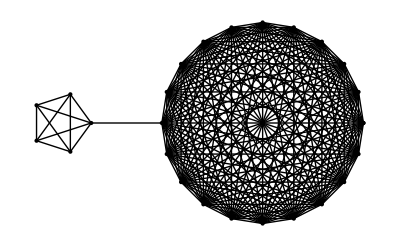

This physics relates to (for example) the thermodynamics of diffusion through one-way membranes.

## Slide 22

# 4. DC Circuit Analysis

Here is a randomly constructed 8-vertex graph

```mathematica
𝕒 = Table[Table[Which[k ⩽ n, 0, k > n, RandomChoice[{0, 1}]], {k, 1, 8}], {n, 1, 8}];
MatrixForm[𝕒]
GraphPlot[𝕒, VertexLabeling -> True]
```

Assign resistances

R_(m,n)=R_(n,m)

to each of the edges and it becomes a DC circuit. Connect one vertex (henceforth "note") to ground (whereupon it becomes an "electrode" or "terminal"), and another to a potential V. The problem then is to compute

   •  the potential V_n at each node;
   •  the current J_(m,n)=-J_(n,m) through each resistor;
   •  the effective resistance R_effective of the network.
   
In favorable cases sauch problems can be solved by simple symmetry arguments. Every first-year student is familiar with, for example, the problem (see Problem 40 on page 702 of D. C. Giancoli, Physics for Scientists & Engineers (2008)) of 12 unit resistors in cubic array:

-Graphics3D-

Such arguments fail, however, when the resistors are assigned arbitrary values (broken symmetry). Students are advised then to appeal to 

  •  Kirchhoff's Node Rule (charge conservation):

∑_(n ∈ Adjacent Nodes) J_(m,n)=0   :   one such statement for each node

•  Kirchhoff's Loop Rule (electrostratic fields are conservative: ∮  E·ds = 0 ):

∑_loop V_n = 0   :   one such statement for each loop—many redundant

•  Ohm's Law

In practice, one (1) assigns arbitrary directionality to the currents

```mathematica
GraphPlot[𝕒, VertexLabeling -> True, DirectedEdges->True]
```

(2) has typically many more currents than nodal potentials to deal with, and (3) has no "most natural" way to select a sufficient set of independent loops…but is led ultimately to a large set of simultaneous linear equations.

I discribe two alternative ways to avoid those difficulties, both of which proceed from this advice:

Forget the currents, forget the loops!

## Slide 23

### Formulate nodal rule in terms of nodal potentials and adjacent conductances:

From

∑_(n ∈ Adjacent Nodes) (V_m-V_n)/R_mn=∑_(n ∈ Adjacent Nodes) c_mn(V_m-V_n)

get (except at the terminal nodes; i.e., at all interior nodes)

V_m=∑_(n ∈ Adjacent Nodes) c_mn/c_m V_n     with     c_m=∑_(n ∈ Adjacent Nodes) c_mn

whence finally the nodal constraint relations

V_m-∑_(n ∈ Adjacent Nodes) c_mn/c_m V_n=(J_(out/in))/c_m

where (if, as a matter of convenience, we assign unit value to the through-current J)

J_(out/in) = ±1 at exit/entry nodes, 0 at interior nodes.


EXAMPLE: Unit resistors in cubic array, diametric electrodes

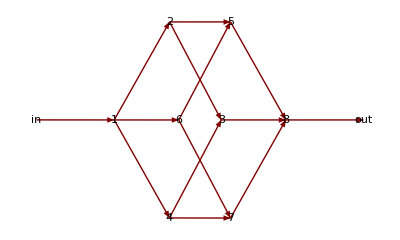

Reading from the graph, we have the adjacency matrix

𝔸_cube=(0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

which I verify:

```mathematica
GraphPlot[({{0, 1, 0, 1, 0, 1, 0, 0}, {1, 0, 1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1, 0, 1}, {0, 0, 1, 0, 1, 0, 1, 0}}), VertexLabeling -> True]
```

The nodal constraint relations can be written

𝕍_unitcube.(V_1
V_2
V_3
V_4
V_5
V_6
V_7
V_8)=(-1/3
0
0
0
0
0
0
+1/3)

where in terms of the "conduction matix" (which is a conductance-weighted variant of the adjacency matrix)

```mathematica
Subscript[ℂ, unitcube]=({{0, 1/3, 0, 1/3, 0, 1/3, 0, 0}, {1/3, 0, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 0, 1/3, 0, 0, 0, 1/3}, {1/3, 0, 1/3, 0, 0, 0, 1/3, 0}, {0, 1/3, 0, 0, 0, 1/3, 0, 1/3}, {1/3, 0, 0, 0, 1/3, 0, 1/3, 0}, {0, 0, 0, 1/3, 0, 1/3, 0, 1/3}, {0, 0, 1/3, 0, 1/3, 0, 1/3, 0}});
```

we have

```mathematica
Subscript[𝕍, unitcube]=IdentityMatrix[8]-Subscript[ℂ, unitcube];
Subscript[𝕍, unitcube]//MatrixForm
```

One might be tempted to suppose that the nodal constraint relations are by themselves sufficient to determine the nodal potentials V_m, but from any of the following statements

```mathematica
Eigenvalues[Subscript[𝕍, unitcube]]
NullSpace[Subscript[𝕍, unitcube]]
MatrixRank[Subscript[𝕍, unitcube]]
```

we infer that we stand in need of one further condition.

## Slide 24

### Principle of Minimal Energy Dissipation (Minimal Entropy Production)

It has always seemed to me to be self-evident that current passing through a resistive DC network will be so partitioned as to minimize the dissipation rate.  It is a proposition which I have assumed to be well known to electrical engineers, and am surprised to discover that as recently as 1999 it was presented in the pages of the American Journal of Physics (D. A. Van Baak, "Variational alternatives to Kirchhoff's loop theorem in dc circuits," AJP 67, 36 (1999)) as something of a novelty. Van Bank does provide, in his Section III, an elaborate "Proof of the Variational Principle," and traces its ancestory all the way back to Maxwell, who in A Treatise on Electricity & Magnetism §§ 283-284 proves that

"In any system of conductors in which there are no internal electromotive forces the heat generated by currents distributed in    accordance with Ohm's Law is less than if the currents had been distributed in any other manner  consistent with the actual conditions of supply and outflow of the current."

Van Baak also cites a comment added by J. J. Thomson as a footnote to Maxwell's §283, §358 in the 5^thedition of J. Jeans'  The Mathematical Theory of Electricity & Magnetism, and the Note which Feynman appended to Chapter 19, "The Principle of Least Action" in Vol. 2 of  The Feynman Lectures on Physics.
 
Here I am content to accept the validity of that variational principle as a given.

We have

DissipationRate=∑_(all branches) R_branch(J^2)_branch

which we must minimize subject to the J_branch-contraints imposed by Kirchhoff's node rule.  

We note in passing that the dissipation function is insensitive to the signs of the branch currents (therefore invariably positive), though the nodal constraints are sign-sensitive. 

It is to illustrate the application of a general variational principle that we look specifically to the case of a cubic array, and it is to verify that the method works that we look first (because in that case we possess a trivially exact solution) to…

#### Dissipation rate & effective resistance of cubic array when all resistors have unit resistance

All resistors have unit value, so

J_(m,n)=V_m-V_n

and the dissipation function becomes

```mathematica
Subscript[Diss, unitcube]=Expand[(Subscript[V, 1]-Subscript[V, 2])^2+(Subscript[V, 1]-Subscript[V, 4])^2+(Subscript[V, 1]-Subscript[V, 6])^2+(Subscript[V, 2]-Subscript[V, 3])^2+(Subscript[V, 2]-Subscript[V, 5])^2+(Subscript[V, 4]-Subscript[V, 7])^2+(Subscript[V, 4]-Subscript[V, 3])^2+(Subscript[V, 6]-Subscript[V, 5])^2+(Subscript[V, 6]-Subscript[V, 7])^2+(Subscript[V, 3]-Subscript[V, 8])^2+(Subscript[V, 5]-Subscript[V, 8])^2+(Subscript[V, 7]-Subscript[V, 8])^2];
Subscript[Diss, unitcube]
```

This is a quadratic form, which in terms of

```mathematica
Subscript[𝔻, unitcube]=({{3, -1, 0, -1, 0, -1, 0, 0}, {-1, 3, -1, 0, -1, 0, 0, 0}, {0, -1, 3, -1, 0, 0, 0, -1}, {-1, 0, -1, 3, 0, 0, -1, 0}, {0, -1, 0, 0, 3, -1, 0, -1}, {-1, 0, 0, 0, -1, 3, -1, 0}, {0, 0, 0, -1, 0, -1, 3, -1}, {0, 0, -1, 0, -1, 0, -1, 3}});
```

can be written

```mathematica
Expand[Transpose[({{Subscript[V, 1]}, {Subscript[V, 2]}, {Subscript[V, 3]}, {Subscript[V, 4]}, {Subscript[V, 5]}, {Subscript[V, 6]}, {Subscript[V, 7]}, {Subscript[V, 8]}})].Subscript[𝔻, unitcube].({{Subscript[V, 1]}, {Subscript[V, 2]}, {Subscript[V, 3]}, {Subscript[V, 4]}, {Subscript[V, 5]}, {Subscript[V, 6]}, {Subscript[V, 7]}, {Subscript[V, 8]}})]⟦1⟧=={Subscript[Diss, unitcube]}
```

From

```mathematica
Eigenvalues[Subscript[𝔻, unitcube]]
```

we see that the dissipation function is constant on 7-dimensional hyper-ellipsoids that live in the 
7-dimensional subspace of 8-dimensional V-space that is orthogonal to

```mathematica
NullSpace[Subscript[𝔻, unitcube]]
```

The nodal constraints (obtained previously) can be written

```mathematica
Subscript[NodalConstraints, unitcube]={
Subscript[V, 1]==(Subscript[V, 2]+Subscript[V, 4]+Subscript[V, 6]+1)/3,
Subscript[V, 2]==(Subscript[V, 1]+Subscript[V, 3]+Subscript[V, 5])/3,
Subscript[V, 3]==(Subscript[V, 2]+Subscript[V, 4]+Subscript[V, 8])/3,
Subscript[V, 4]==(Subscript[V, 1]+Subscript[V, 3]+Subscript[V, 7])/3,
Subscript[V, 5]==(Subscript[V, 2]+Subscript[V, 6]+Subscript[V, 8])/3,
Subscript[V, 6]==(Subscript[V, 1]+Subscript[V, 5]+Subscript[V, 7])/3,
Subscript[V, 7]==(Subscript[V, 4]+Subscript[V, 6]+Subscript[V, 8])/3,
Subscript[V, 8]==(Subscript[V, 3]+Subscript[V, 5]+Subscript[V, 7]-1)/3};
```

Thus prepared, we command

```mathematica
Minimize[Flatten[{{Subscript[Diss, unitcube]},Subscript[NodalConstraints, unitcube]}],{Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],Subscript[V, 7],Subscript[V, 8]}]
```

and recover precisely the results yielded by the elementary symmetry argument.

I suspect that the variational method has been relatively neglected because minimization problems can be difficult to solve by hand. But for Mathematica they are a piece of cake.

From

dissipation=R_effective J^2  + fact that we have assumed J=1

we see that for the unit cube (with diametric electrodes)

R_effective=5/6

Other values of the through-current J (equivalently: of the impressed potential) are obtained by trivial rescaling.

### Next-to-adjacent electrodes

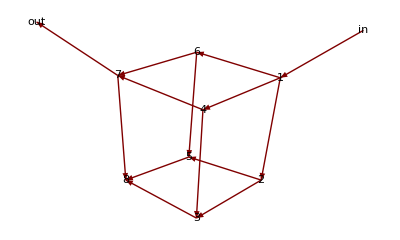

Trivial modification of the nodal constraint relations

```mathematica
Subscript[NodalConstraints, unitcube2]={
Subscript[V, 1]==(Subscript[V, 2]+Subscript[V, 4]+Subscript[V, 6]+1)/3,
Subscript[V, 2]==(Subscript[V, 1]+Subscript[V, 3]+Subscript[V, 5])/3,
Subscript[V, 3]==(Subscript[V, 2]+Subscript[V, 4]+Subscript[V, 8])/3,
Subscript[V, 4]==(Subscript[V, 1]+Subscript[V, 3]+Subscript[V, 7])/3,
Subscript[V, 5]==(Subscript[V, 2]+Subscript[V, 6]+Subscript[V, 8])/3,
Subscript[V, 6]==(Subscript[V, 1]+Subscript[V, 5]+Subscript[V, 7])/3,
Subscript[V, 7]==(Subscript[V, 4]+Subscript[V, 6]+Subscript[V, 8]-1)/3,
Subscript[V, 8]==(Subscript[V, 3]+Subscript[V, 5]+Subscript[V, 7])/3};
```

supplies

```mathematica
Minimize[Flatten[{{Subscript[Diss, unitcube]},Subscript[NodalConstraints, unitcube2]}],{Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],Subscript[V, 7],Subscript[V, 8]}]
```

### Next-to-adjacent electrodes

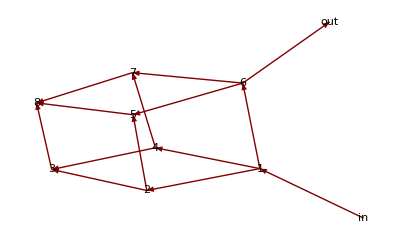

```mathematica
Subscript[NodalConstraints, unitcube3]={
Subscript[V, 1]==(Subscript[V, 2]+Subscript[V, 4]+Subscript[V, 6]+1)/3,
Subscript[V, 2]==(Subscript[V, 1]+Subscript[V, 3]+Subscript[V, 5])/3,
Subscript[V, 3]==(Subscript[V, 2]+Subscript[V, 4]+Subscript[V, 8])/3,
Subscript[V, 4]==(Subscript[V, 1]+Subscript[V, 3]+Subscript[V, 7])/3,
Subscript[V, 5]==(Subscript[V, 2]+Subscript[V, 6]+Subscript[V, 8])/3,
Subscript[V, 6]==(Subscript[V, 1]+Subscript[V, 5]+Subscript[V, 7]-1)/3,
Subscript[V, 7]==(Subscript[V, 4]+Subscript[V, 6]+Subscript[V, 8])/3,
Subscript[V, 8]==(Subscript[V, 3]+Subscript[V, 5]+Subscript[V, 7])/3};
```

```mathematica
Minimize[Flatten[{{Subscript[Diss, unitcube]},Subscript[NodalConstraints, unitcube3]}],{Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],Subscript[V, 7],Subscript[V, 8]}]
```

As expected, moving electrodes closer together has served in each instance to reduce the effective resistance:

```mathematica
5/6>3/4>7/12
```

## Slide 25

### Digression: Contact with the Theory of Harmonic Functions (Potential Theory)

For the unit cube we had (for example)

V_2=(V_1+V_3+V_5)/3=average of adjacent potentials

and more generally

V_m=∑_(n ∈ Adjacent Nodes) c_mn/c_m V_n=weighted average of adjacent potentials

These are discrete analogs of the statement

∇^2 V(x,y,z)=0

that V (x, y, z) is a "harmonic function"—the central object in "potential theory."


Functions that are harmonic on 𝒟 assume their extremal values on the boundary of 𝒟. We therefore expect (and observed) that nodal potentials are extremal at the electrodes.

## Slide 26

### Cubic array with ARBITRARY CONDUCTANCES (resistances)

Assume for the moment that the circuit is disconnected (all nodes are "interior," none have been pressed into service as "electrodes"). Feeding

V_m=∑_(n ∈ Adjacent Nodes) c_mn/c_m V_n

into the cubic adjacency matrix

𝔸_cube=(0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

(which remains unchanged) we obtain

(V_1
V_2
V_3
V_4
V_5
V_6
V_7
V_8)=ℂ_cube.(V_1
V_2
V_3
V_4
V_5
V_6
V_7
V_8)

with

ℂ_cube=(0 | c_12/(c_12+c_14+c_16) | 0 | c_14/(c_12+c_14+c_16) | 0 | c_16/(c_12+c_14+c_16) | 0 | 0
c_21/(c_21+c_23+c_25) | 0 | c_23/(c_21+c_23+c_25) | 0 | c_25/(c_21+c_23+c_25) | 0 | 0 | 0
0 | c_32/(c_32+c_34+c_38) | 0 | c_34/(c_32+c_34+c_38) | 0 | 0 | 0 | c_38/(c_32+c_34+c_38)
c_41/(c_41+c_43+c_47) | 0 | c_43/(c_41+c_43+c_47) | 0 | 0 | 0 | c_47/(c_41+c_43+c_47) | 0
0 | c_52/(c_52+c_56+c_58) | 0 | 0 | 0 | c_56/(c_52+c_56+c_58) | 0 | c_58/(c_52+c_56+c_58)
c_61/(c_61+c_65+c_67) | 0 | 0 | 0 | c_65/(c_61+c_65+c_67) | 0 | c_67/(c_61+c_65+c_67) | 0
0 | 0 | 0 | c_74/(c_74+c_76+c_78) | 0 | c_76/(c_74+c_76+c_78) | 0 | c_78/(c_74+c_76+c_78)
0 | 0 | c_83/(c_83+c_85+c_87) | 0 | c_85/(c_83+c_85+c_87) | 0 | c_87/(c_83+c_85+c_87) | 0);

Notice that—though

c_mn=c_nm

—the symmetry of ℂ_cube is (except in special cases, like the unit cube) destroyed by the demonimators. Note also that

the elements in each row sum to unity

i.e., that

Transpose[ℂ_cube]possesses the characteristic stucture of a  transition matrix

The dissipation function has become

```mathematica
Clear[c]
Subscript[Diss, cube]=Expand[Subscript[c, 12](Subscript[V, 1]-Subscript[V, 2])^2+Subscript[c, 14](Subscript[V, 1]-Subscript[V, 4])^2+Subscript[c, 16](Subscript[V, 1]-Subscript[V, 6])^2+Subscript[c, 23](Subscript[V, 2]-Subscript[V, 3])^2+Subscript[c, 25](Subscript[V, 2]-Subscript[V, 5])^2+Subscript[c, 47](Subscript[V, 4]-Subscript[V, 7])^2+Subscript[c, 43](Subscript[V, 4]-Subscript[V, 3])^2+Subscript[c, 65](Subscript[V, 6]-Subscript[V, 5])^2+Subscript[c, 67](Subscript[V, 6]-Subscript[V, 7])^2+Subscript[c, 38](Subscript[V, 3]-Subscript[V, 8])^2+Subscript[c, 58](Subscript[V, 5]-Subscript[V, 8])^2+Subscript[c, 78](Subscript[V, 7]-Subscript[V, 8])^2];
Subscript[Diss, cube]
```

From this point the argument proceeds exactly as before. 

For arbitrary circuits one proceeds from a different adjacency matrix, with resistances peculiar to that circuit, but the pattern of the argument is unchanged. 

It is easy to devise simple commands that proceed automatically from the adjacency matrix, resistor list and specified electrode locations to the construction of the nodal constraints and dissipation function.

## Slide 27

### Adventures of an "electron" strolling randomly on a DC circuit

I turn finally to an idea first adumbrated by S. Katutani, "Markov processes and the Direchlet problem," Proc. Jap. Acad. 21, 227-233 (1945), developed by C. St.  J. A. Nash-Williams, "Random walk and electric currents in networks," Proc. Camb. Phil. Soc. 55, 181-194 (1959), and discussed in elaborate detail by Peter G. Doyle & J. Laurie Snell in Random Walks and Electric Networks, originally published in 1984 by the Mathematical Association of America (Carus Mathematical Monograph No. 22), now available on the web

```mathematica
Hyperlink["Doyle & Snell","http://www.stanford.edu/class/msande337/notes/walks.pdf"]
```

in a version dated 5 July 2006.

I develop this subject as it relates specifically to a cubic array of unit resistors.

Let

P_n=probability that an "electron" —    walking randomly on the given circuit — will reach the input node before visiting the grounded node

Clearly,

P_input=1
P_output=0

Let

prob_(m,n)=probability of transition m⟶n

On statistical independence grounds we then have

P_m=∑_(n ∈ AdjacentNodes) prob_(m,n)P_n

Set (which seems intuitively plausible)

t_(m,n)=c_mn/c_m   :   "fractional conductance" away from m^th node

and assume

V=V_impressed-V_ground=1

Comparison of

P_m=∑_(n ∈ AdjacentNodes) c_mn/c_m P_n
V_m=∑_(n ∈ AdjacentNodes) c_mn/c_m V_n

establishes an association P_m⟷V_m.

Introducing vectors (zero-entropy stochastic vectors)

```mathematica
Subscript[σ, 1]={1,0,0,0,0,0,0,0};
Subscript[σ, 2]={0,1,0,0,0,0,0,0};
Subscript[σ, 3]={0,0,1,0,0,0,0,0};
Subscript[σ, 4]={0,0,0,1,0,0,0,0};
Subscript[σ, 5]={0,0,0,0,1,0,0,0};
Subscript[σ, 6]={0,0,0,0,0,1,0,0};
Subscript[σ, 7]={0,0,0,0,0,0,1,0};
Subscript[σ, 8]={0,0,0,0,0,0,0,1};
```

to distinguish one node from another, we contemplate the adventure of a walker—"Electron"—who strolls about the circuit making site-specific next-step decisions based upon the information written into the structure of the transition matrix

𝕋_cube=Transpose[ℂ_cube]//MatrixForm

(0 | c_21/(c_21+c_23+c_25) | 0 | c_41/(c_41+c_43+c_47) | 0 | c_61/(c_61+c_65+c_67) | 0 | 0
c_12/(c_12+c_14+c_16) | 0 | c_32/(c_32+c_34+c_38) | 0 | c_52/(c_52+c_56+c_58) | 0 | 0 | 0
0 | c_23/(c_21+c_23+c_25) | 0 | c_43/(c_41+c_43+c_47) | 0 | 0 | 0 | c_83/(c_83+c_85+c_87)
c_14/(c_12+c_14+c_16) | 0 | c_34/(c_32+c_34+c_38) | 0 | 0 | 0 | c_74/(c_74+c_76+c_78) | 0
0 | c_25/(c_21+c_23+c_25) | 0 | 0 | 0 | c_65/(c_61+c_65+c_67) | 0 | c_85/(c_83+c_85+c_87)
c_16/(c_12+c_14+c_16) | 0 | 0 | 0 | c_56/(c_52+c_56+c_58) | 0 | c_76/(c_74+c_76+c_78) | 0
0 | 0 | 0 | c_47/(c_41+c_43+c_47) | 0 | c_67/(c_61+c_65+c_67) | 0 | c_87/(c_83+c_85+c_87)
0 | 0 | c_38/(c_32+c_34+c_38) | 0 | c_58/(c_52+c_56+c_58) | 0 | c_78/(c_74+c_76+c_78) | 0)

To illustrate the process, we look specifically (once again) to case in which all conductances are unity:

```mathematica
Subscript[𝕋, unitcube]=({{0, 1/3, 0, 1/3, 0, 1/3, 0, 0}, {1/3, 0, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 0, 1/3, 0, 0, 0, 1/3}, {1/3, 0, 1/3, 0, 0, 0, 1/3, 0}, {0, 1/3, 0, 0, 0, 1/3, 0, 1/3}, {1/3, 0, 0, 0, 1/3, 0, 1/3, 0}, {0, 0, 0, 1/3, 0, 1/3, 0, 1/3}, {0, 0, 1/3, 0, 1/3, 0, 1/3, 0}});
```

An electron who stands momentarily at σ_m will base its next-step decision upon information written into the m^th column of 𝕋_unitcube (which is the m^th row of ℂ_unitcube), to which we give a name:

```mathematica
Table[Subscript[T, m]=Subscript[ℂ, unitcube]⟦m⟧,{m,1,8}];
```

Thus

```mathematica
Subscript[T, 1]
Subscript[T, 2]
```

Here we generate "by hand" a 5-step walk—a different walk each time the command is repeated—that departs from σ_3:

```mathematica
Subscript[σ, 3]
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
```

If, however, we have interest in many long walks then that "by hand" procedure becomes excessively tedious; here I provide an automated procedure (which is computationally quicker, and has neater output):

```mathematica
NestList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 3],10]//TableForm
```

Slight modification of that command generates walks that automatically terminate when Electron first arrives at a designated node (taken here to be σ_1). Here I generate a list of 20 such terminated walks:

```mathematica
Table[{Subscript[Walk, n]=NestWhileList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 3],#≠{1,0,0,0,0,0,0,0}&]},{n,1,20}];
```

and display a representative few of those walks:

```mathematica
Table[{j,Subscript[Walk, j]},{j,10,15}]//TableForm
```

Observe that all walks begin at σ_3, all terminate at σ_1, some are long, some short, some visit (say) σ_8 one or more times while en route σ_3⟶σ_1, some don't.

## Slide 28

### Monte Carlo estimation of a nodal potential

We look again to the case unit resistors in cubic array, with electrodes placed as shown:

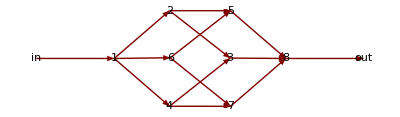

We assume that V_1=1, V_8=0 and ask for the value of V_3. That is equivalent to asking for the probability that Electron, departing from node σ_3, will arrive at σ_1 without having visited σ_8.

To obtain an estimate of that probability, we (as proof of method) construct 100 walks  σ_3⟶σ_1

```mathematica
Table[{Subscript[Walk, n]=NestWhileList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 3],#≠{1,0,0,0,0,0,0,0}&]},{n,1,100}];
```

and resolve them into two groups: "A walks" that successfully avoid the grounded node σ_8 and "B-walks" that don't:

```mathematica
Clear[A,B]
```

```mathematica
Table[Which[Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]==0,A,Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]!=0,B],{j,1,100}]
```

```mathematica
Tally[%]
```

On that basis we have

V_3~ProbOfSuccess_(3→1)=30/100=.30

which is a poor approximation to the exact V_3= 2/5=.40 to which the symmetry argument and variational method both lead. To improve the accuracy of Monte Carlo calculations one increases the size of the sample. For a 10,000-walk sample we get

```mathematica
Table[{Subscript[Walk, n]=NestWhileList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 3],#≠{1,0,0,0,0,0,0,0}&]},{n,1,10000}];
Table[Which[Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]==0,A,Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]!=0,B],{j,1,10000}];
Tally[%]
```

V_3~.4047

in which the error has been reduced to nearly the 1% level.

Each of the other nodal potentials requires a separate (but similar) calculation.

The method easily accommodates circuits of arbitrary design, with arbitrary resistances.

Would seem a silly way to analyize simple circuits, but from the web I gather that similar Monte Carlo methods are standardly used to study
   • circuits with millions of components
   • power grids, etc. 
   
The importance of the method is mainly theoretical. Reuben Hersh & Richard J. Griego, in their frequently-cited article "Brownian Motion & Potential Theory" (Scientific American 220, 67-74, March 1969), state that

"One of the most exciting events of the past decade or so in the field of mathematical analysis has been the appearance of a new subject called probabilistic potential theory. In essence this subject represents the marriage of two major branches of theoretical physics… "

Of lesser importance is the fact that the method leads to a novel interpretation to the concept of "electric current": J_(m, n) becomes a measure of how much the "walking Electron traffic"  m⟶n  exceeds that in the opposite direction: m⟵n.

## Slide 29

# 5. Opened Doors

### Percolation Theory

Drop a number N of unit resistors randomly onto network of terminals (with designated terminals serving as electrodes) and ask for the N-dependence of the mean value of R_effective.

I describe two ways to generate such random DC networks and, in each case, of counting the number of resistors:

```mathematica
Needs["Combinatorica`"]
```

The following commands (1) generate—with each repetition— a 20-node graph, (2) installs edges randomly with probability 0.05, (3) counts the number of edges, and finally (4) draws the graph:

```mathematica
g=RandomGraph[20,.05];
Edges[g]
Length[Edges[g]]
ShowGraph[g]
```

The following command draws 20-node graphs in which the edge probability ranges randomly from 0 to 1 in 0.02 increments:

```mathematica
Manipulate[RandomGraph[20,p]//ShowGraph,{p,0,1,.02}]
```

Calculations that employ the variational method to evaluate R_effectiveproceed more naturally from commands that construct (the above-diagonal sectors of) random adjacency matrices. Define

```mathematica
R[p_]:=Which[0⩽x⩽p,1,p<x⩽1,0]/.x->RandomReal[]

𝕒[p_] :=Table[Table[Which[k ⩽ n, 0, k > n, R[p]], {k, 1, 10}], {n, 1, 10}];
```

(here p controls the probability that 1s appear in the adjacency matrix) and repeatedly enter p-adjusted variants of the following commands:

```mathematica
MatrixForm[𝕒[.3]]
Total[Flatten[%]]
GraphPlot[%%, VertexLabeling -> True]
```

The adjacency matrix itself is

```mathematica
𝔸=MatrixForm[%%%+Transpose[%%%]]
```

in which every edge is recorded twice (m⟶n and m⟵n).

### "The classical mechanics of non-classical systems"—revisited

That was the title of my own Reed thesis. The idea was to use the .08Hamiltonian H(x, p) to deposit site-specific next-step probabilistics on a discretized phase space

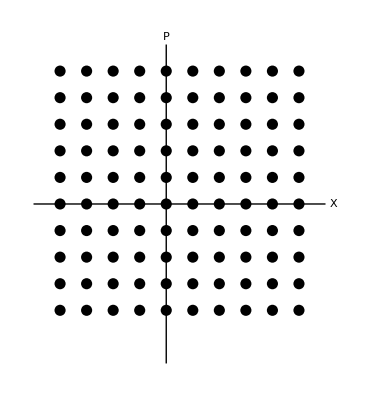

in such a way that the mean position of many walkers—all of whom depart from (x_0,p_0)—moves in accordance with Hamilton's equations of motion. I seem finally—after 56 years!—to be in position to address the problem.

One might expect to establish contact with the theory of stochastic differential equations.

### Finite-dimensional Supersymmetric Quantum Mechanics

Exposure to "supersymmetric (or Wishart) matrices" has motivated me to develop the rudiments of a "finite-dimensional supersymmetric quantum mechanics" in which Hamiltonians have the structure

```mathematica
ℍ=({{SuperPlus[𝔸].𝔸, 𝕆}, {𝕆, 𝔸.SuperPlus[𝔸]}})
```

### Quantum walks & quantum mechanical circuit theory

From here it is but a short step to the quantum walks that have recently engaged the interest of quantum computation theorists

```mathematica
Hyperlink["Quantum Walks","http://en.wikipedia.org/wiki/Quantum_walk"]
```

```mathematica
Hyperlink["Papers by Andrew Childs","http://www.math.uwaterloo.ca/~amchilds/papers/"]
```

Quantum walk physics has been used also to account for the surprising efficiency of photosynthesis:

```mathematica
Hyperlink["Quantum Walks in Photosynthetic Energy Transfer","http://aspuru.unix.fas.harvard.edu/uploads/QW-FMO-JCPSA612917174106_1.pdf"]
```

```mathematica
Hyperlink["Papers by Cesar Rodriguez-Rosario","http://aspuru.chem.harvard.edu/People/Cesar_Rodriguez/"]
```

[Both Childs and Rodriguez-Rosario were, by the way, recent applicants for positions on the Reed College physics faculty.]

Somewhat longer steps lead to aspects of quantum circuit theory :

```mathematica
Hyperlink["Quantum Fluctuations in Electrical Circuits","http://qulab.eng.yale.edu/documents/reprints/Houches_fluctuations.pdf"]
```

```mathematica
Hyperlink["Chronobiological Applications of QM Circuit Theory","http://arxiv.org/pdf/1110.2637"]
```

### Blinkers

The transition matrix of a unit cube

```mathematica
Subscript[𝕋, unitcube]=({{0, 1/3, 0, 1/3, 0, 1/3, 0, 0}, {1/3, 0, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 0, 1/3, 0, 0, 0, 1/3}, {1/3, 0, 1/3, 0, 0, 0, 1/3, 0}, {0, 1/3, 0, 0, 0, 1/3, 0, 1/3}, {1/3, 0, 0, 0, 1/3, 0, 1/3, 0}, {0, 0, 0, 1/3, 0, 1/3, 0, 1/3}, {0, 0, 1/3, 0, 1/3, 0, 1/3, 0}});
```

possesses the curious property that it gives rise not to a single (equilibrated) asymptotic state, but to a pair of states that "blink":

```mathematica
Table[MatrixForm[N[MatrixPower[Subscript[𝕋, unitcube],k].({{1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}})]],{k,10,15}]
```

This can be traced to the fact that ±1 both appear among its eigenvalues:

```mathematica
Eigenvalues[Subscript[𝕋, unitcube]]
```

The (unitized) leading eigenvector is recovered as the average of the blinking states:

```mathematica
Transpose[{N[(Eigenvectors[Subscript[𝕋, unitcube]]⟦2⟧)/Total[Eigenvectors[Subscript[𝕋, unitcube]]⟦2⟧]]}]//MatrixForm
```

Blinking, whenever it arises, always reflects that circumstance that the walker has only to compare the "color" of the node on which he stands to the color of the node from which he departed to determine whether he has taken an even/odd number of steps in arriving there, and is by no means uncommon:

Even—and somewhat surprisingly?—walks performed on certain Penrose tilings blink. This "kites & darts" tiling blinks

but this "fat & skinny parallelogram" tiling

does not.

## End

◀     |     ▶